```mathematica
Nt = 551; (*1000 -> default*)(*10 -> simple case to compare to reduced points*)
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*500 default from problem*)(*200 -> my choice*) (*25 -> simple case to compare to reduced points*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax);

(*For Eigenvalue Plots in Complex Plane*)
(*rs = {0.9,1,1.1};*)
(*rs = {1.4,1.5,1.6};*)(*When exporting RK4 and LD4*)

(*For Max Eigenvalue Plots*)
rs = Table[0.01*i,{i,1,30}];

finalerrorCN = Table[0,{i,1,Length[rs]}];
finalerrorEuler = Table[0,{i,1,Length[rs]}];
finalerrorRK2 = Table[0,{i,1,Length[rs]}];
finalerrorRK4 = Table[0,{i,1,Length[rs]}];
finalerrorLD4 = Table[0,{i,1,Length[rs]}];

f[x_] =ⅇ^(- 8(x-π)^2);
```

```mathematica
Dimensions[MN]
```

{551,551}

```mathematica
Do[
deltat = deltax * rs[[p]];

T = Table[tn = ti + n *deltat, {n, 0, Nt -1}]//N;

(*For Perodic Interpolation*) 
Xp= Table[xm = xi + m *deltax, {m, 0, Nx}]//N;

X= Table[xm = xi + m *deltax, {m, 0, Nx - 1}]//N;


L11 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L11//MatrixForm;
DL11 = -c * L11 * deltat;

L12 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL12 = -c * L12 * deltat;

L22 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL22 = (-c)^2 * L22 * (deltat)^2;

L14 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L14//MatrixForm;
DL14 = -c * L14 * deltat;

L24 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L24//MatrixForm;
DL24 = (-c)^2 * L24 * (deltat)^2;

L34 = (NDSolve`FiniteDifferenceDerivative[Derivative[3],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL34 = (-c)^3 * L34 * (deltat)^3;

L44 = (NDSolve`FiniteDifferenceDerivative[Derivative[4],Xp, "DifferenceOrder"->4, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
DL44 = (-c)^4 * L44 * (deltat)^4;


(* Crank-Nicolson *)
UCN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UCN[[1,All]] = f[X]//N;
UCN = Chop[N[UCN], 10^(-307)];
UCN = N[UCN];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN];


I1 = IdentityMatrix[Length[DL12]];
A = I1 - ((DL12 / 2));
B = I1 + ((DL12 / 2));
MCN = Inverse[A].B;

Do[UCN[[n+1,All]] = UCN[[n,All]] + (MCN - I1).UCN[[n,All]], {n,1,Nt - 1 }];

FCN = Table[0,{i,1,Nt},{j,1,Nx}];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
Do[
FCN[[i,All]] = (L12.UCN[[i,All]])^2;

intCN[[i]] = (xf - xi)/Nx Total[FCN[[i,All]]];
,{i,1,Length[FCN[[All,1]]]}];

finalerrorCN[[p]] =Abs[Last[intCN] - intCN[[1]]]; 



(*RK2*)
URK2= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK2[[1,All]] = f[X]//N;
URK2 = Chop[N[URK2], 10^(-307)];
URK2 = N[URK2];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2];

IRK2 = IdentityMatrix[Length[DL12]];

MRK2 = (IRK2 + (DL12) + ((1/2)*(DL22)));

Do[URK2[[n+1,All]] = URK2[[n,All]] + (MRK2 - IRK2).URK2[[n,All]], {n,1,Nt - 1 }];

FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
Do[
FRK2[[i]] = (L12.URK2[[i,All]])^2;

intRK2[[i]] = (xf-xi)/Nx Total[FRK2[[i,All]]];
,{i,1,Length[FRK2[[All,1]]]}];

finalerrorRK2[[p]] =Abs[Last[intRK2] - intRK2[[1]]];

(*RK4*)
URK4= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK4[[1,All]] = f[X]//N;
URK4 = Chop[N[URK4], 10^(-307)];
URK4 = N[URK4];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4];

IRK4 = IdentityMatrix[Length[DL14]];

MRK4 = IRK4 + DL14 + ((1/2) * (DL24)) + ((1/6) * (DL34)) + ((1/24) * (DL44));

Do[URK4[[n+1,All]] = URK4[[n,All]] + (MRK4 - IRK4).URK4[[n,All]], {n,1,Nt - 1 }];

FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
Do[
FRK4[[i]] = (L14.URK4[[i,All]])^2;

intRK4[[i]] = (xf-xi)/Nx Total[FRK4[[i,All]]];
,{i,1,Length[FRK4[[All,1]]]}];

finalerrorRK4[[p]] =Abs[Last[intRK4] - intRK4[[1]]];

(*LD4*)
UN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UN[[1,All]] = f[X]//N;
UN = Chop[N[UN], 10^(-307)];
UN = N[UN];
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN];


IN = IdentityMatrix[Length[DL14]];
AN = IN - ((DL14 / 2)) + (((DL24)/12));
BN = IN + ((DL14 / 2)) + (((DL24)/12));
MN = Inverse[AN].BN;


Do[UN[[n+1,All]] = UN[[n,All]] + (MN - IN).UN[[n,All]], {n,1,Nt - 1 }];

FN = Table[0,{i,1,Nt},{j,1,Nx}];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
Do[
FN[[i]] = (L14.UN[[i,All]])^2;

intN[[i]] = (xf-xi)/Nx Total[FN[[i,All]]];
,{i,1,Length[FN[[All,1]]]}];

finalerrorLD4[[p]] =Abs[Last[intN] - intN[[1]]];


(*For Eigenvalue Plots in Complex Plane*)
(*exportData=Flatten/@Transpose[{realEvalsLD4, imagEvalsLD4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_circle_LD4_"<>ToString[rs[[p]]]<>".dat",exportData,"Table"];*)



,{p,1,Length[rs]}]

(*maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];*)

(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

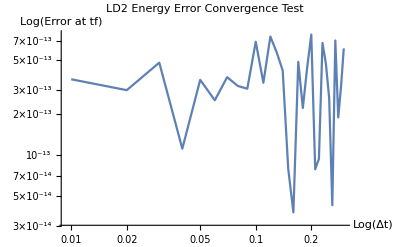

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorCN}], Joined->True,PlotLabel->"LD2 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

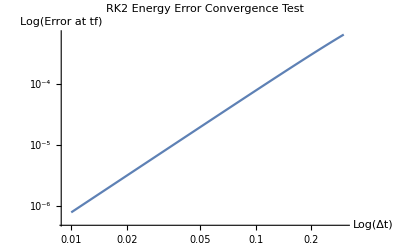

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorRK2}], Joined->True,PlotLabel->"RK2 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

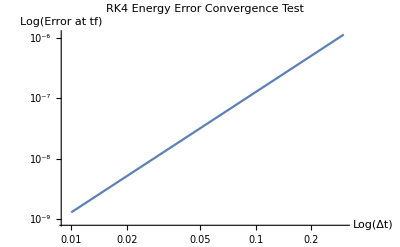

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorRK4}], Joined->True,PlotLabel->"RK4 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

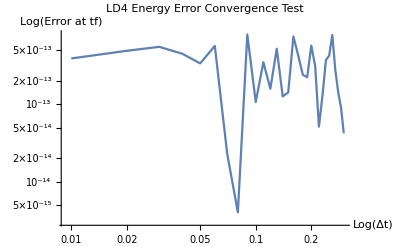

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,finalerrorLD4}], Joined->True,PlotLabel->"LD4 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```